```mathematica
test630=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\1000umclistaltalt.txt","Table"];
```

```mathematica
test6300=test630[[All,{1,2,3,6,7,9,10,11,12,13}]];
```

```mathematica
test6300[[2;;Length[test6300],{1,2,3,4,5,6}]]=Round[test6300[[2;;Length[test6300],{1,2,3,4,5,6}]]];
```

```mathematica
test6300[[2;;Length[test6300],{8}]]=N[test6300[[2;;Length[test6300],{8}]]-750];
```

```mathematica
test6300[[2;;Length[test6300],{10}]]=N[test6300[[2;;Length[test6300],{10}]]-963];
```

```mathematica
test6300[[2;;Length[test6300],{3}]]=N[test6300[[2;;Length[test6300],{3}]]*1/60];
```

```mathematica
test6300cut=removefljumps[test6300];
```

RFP Mean = -0.65333
RFP high = 194.137
RFP max = 1437.65
RFP low = -195.444
RFP min = -1404.55
YFP mean = -0.0847033
YFP high = 124.542
YFP max = 139.406
YFP low = -124.711
YFP min = -152.263

```mathematica
linstest6300cut=lineagefinder[test6300cut];//AbsoluteTiming
```

{18.4527,Null}

```mathematica
comblintest630=combinelineages2fl[test6300,linstest6300cut];//AbsoluteTiming
```

{36.4748,Null}

```mathematica
comblinmultiplytest630=combinelineagesmulitply2fl[test6300,linstest6300cut];//AbsoluteTiming
```

{34.19,Null}

```mathematica
growthtest630noextrap=growthratecalcsupnoextrap[comblinmultiplytest630,30,comblintest630];//AbsoluteTiming
```

387

{5.76435,Null}

```mathematica
testset=RandomChoice[Table[i,{i,1,320}],50]
```

{252,65,293,172,148,114,31,74,216,287,225,34,120,164,156,160,261,29,150,202,160,203,148,277,137,14,40,191,174,224,43,210,46,214,104,93,187,268,149,286,171,184,4,93,120,112,23,223,208,119}

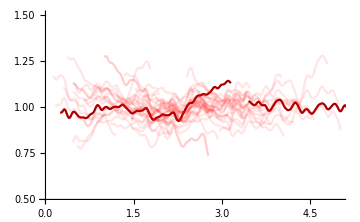

```mathematica
Show[{ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,1]&,{313,123}],PlotRange->{{0,5},{0.5,1.5}},PlotStyle->Darker[Red],ImageSize->Medium,AxesStyle->Directive[Black,20]],ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,1]&,testset],PlotRange->All,PlotStyle->Directive[Opacity[0.1],Red]]}]
```

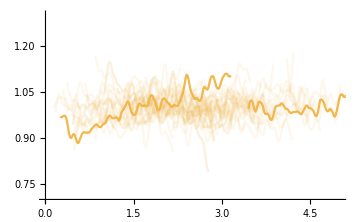

```mathematica
Show[{ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,3]&,{313,123}],PlotRange->{{0,5},{0.7,1.3}},PlotStyle->RGBColor["#f2b74d"],ImageSize->Medium,AxesStyle->Directive[Black,20]],ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,3]&,testset],PlotRange->All,PlotStyle->Directive[Opacity[0.1],RGBColor["#f2b74d"]]]}]
```

```mathematica
{iptg1mmgrowthACF30minwindowsmooth,iptg1mmmcACF30minwindowsmooth,iptg1mmbetaxACF30minwindowsmooth,iptg1mmmcgrowthCCCF30minwindowsmooth,iptg1mmbetaxgrowthCCCF30minwindowsmooth,iptg1mmmcbetaxCCCF30minwindowsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\New folder\\1mmiptgacfcccf30minwindowsmoothfull.txt","Table"];
```

```mathematica
metabsim=metabgensteadystate[0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{472.106,Null}

```mathematica
keepMetabSS=keepallmetabmaintainsteadystate[metabsim[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{1181.14,Null}

```mathematica
metabsimMemory=metabproteinmemfast[keepMetabSS];
```

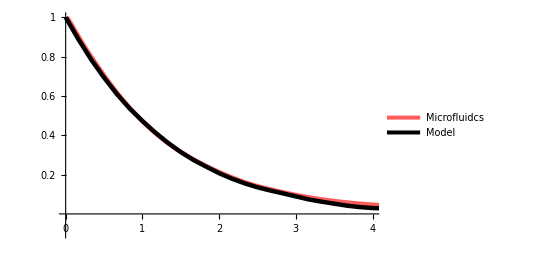

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,1,Length[iptg1mmmcACF30minwindowsmooth]}],iptg1mmmcACF30minwindowsmooth},Map[{#[[1]],#[[2]]}&,metabsimMemory[[1]]]},PlotRange->{{0,4},{-.1,1}},PlotLegends->Placed[{"Microfluidcs","Model"},Right],PlotStyle->{{Thickness[0.008],RGBColor[1,0.36,0.36]},{Thickness[0.008],Black}},AxesStyle->Directive[Black, 20],Ticks->{Automatic,{0.2,0.4,0.6,0.8,1}},AspectRatio->.65]
```

```mathematica
{iptg1000um630growthACFsmooth,iptg1000um630mcACFsmooth,iptg1000um630betaxACFsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\New folder\\1000um630ACFsmooth.txt","Table"];
```

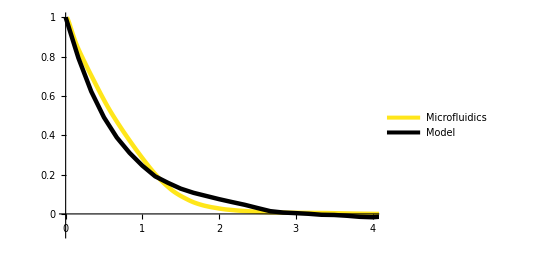

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,1,Length[iptg1000um630betaxACFsmooth]}],iptg1000um630betaxACFsmooth},Map[{#[[1]],#[[2]]}&,metabsimMemory[[3]]]},PlotRange->{{0,4},{-.1,1}},
PlotLegends->Placed[{"Microfluidics","Model"},Right],
PlotStyle->{{Thickness[0.008],RGBColor[1,0.9,0.1]},{Thickness[0.008],Black}},AxesStyle->Directive[Black, 20],Ticks->{Automatic,{0,0.2,0.4,0.6,0.8,1}},AspectRatio->.65]
```

```mathematica
exp227rawdata=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\iptg1mmrawtxt.txt","Table"];//AbsoluteTiming
```

{3.65076,Null}

```mathematica
testexp227cut=removefljumps[exp227rawdata];
```

RFP Mean = -0.438949
RFP high = 812.338
RFP max = 18401.5
RFP low = -813.215
RFP min = -23766.4
YFP mean = -0.0150807
YFP high = 153.572
YFP max = 1288.14
YFP low = -153.602
YFP min = -1250.99

```mathematica
linstestexp227cut=lineagefinder[testexp227cut];//AbsoluteTiming
```

{46.3093,Null}

```mathematica
combliniptg1mm=combinelineages2fl[exp227rawdata,linstestexp227cut];//AbsoluteTiming
```

{131.42,Null}

```mathematica
lowprodmc=Join[combliniptg1mm[[180]][[77;;Length[combliniptg1mm[[180]]],6]],combliniptg1mm[[181]][[All,6]]];
```

```mathematica
lowprodbx=Join[combliniptg1mm[[180]][[77;;Length[combliniptg1mm[[180]]],7]],combliniptg1mm[[181]][[All,7]]];
```

```mathematica
midprodmc=Join[combliniptg1mm[[84]][[29;;Length[combliniptg1mm[[84]]],6]],combliniptg1mm[[85]][[All,6]]];
```

```mathematica
midprodbc=Join[combliniptg1mm[[84]][[29;;Length[combliniptg1mm[[84]]],7]],combliniptg1mm[[85]][[All,7]]];
```

```mathematica
highprodmc=combliniptg1mm[[100]][[All,6]];
```

```mathematica
highprodbx=combliniptg1mm[[100]][[All,7]];
```

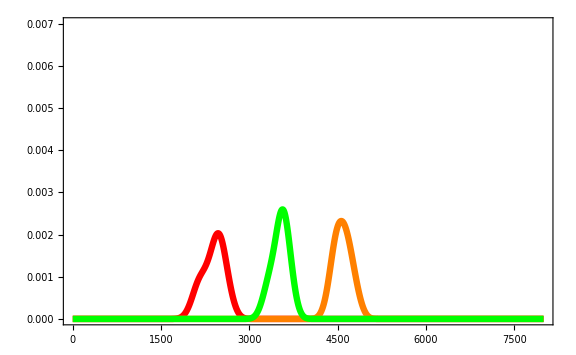
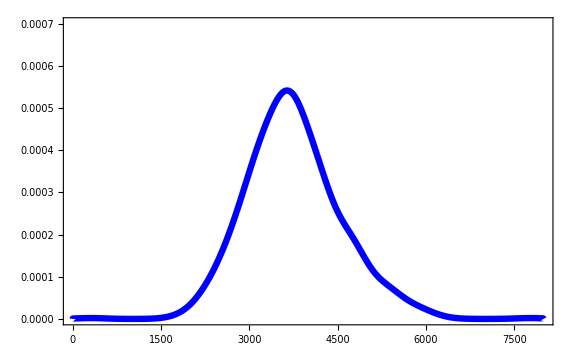
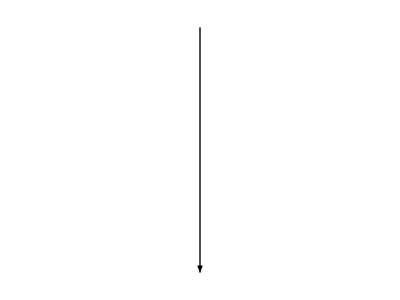

```mathematica
Overlay[{SmoothHistogram[{lowprodmc,midprodmc,highprodmc},100,PlotRange->{{0,8000},{0,0.007}},PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Orange},{Thickness[0.008],Green}},ImageSize->Large,Frame->{True,False,False,False},FrameStyle->Directive[Black,25]],SmoothHistogram[Map[combliniptg1mm[[#]][[1,6]](*/3770*)&,Table[i,{i,Length[combliniptg1mm]}]],250,PlotRange->{{0,8000},{0,0.0007}},PlotStyle->{Thickness[0.008],Blue},ImageSize->Large,Frame->{True,False,False,False,False},FrameStyle->Directive[Black,25]]}]
```

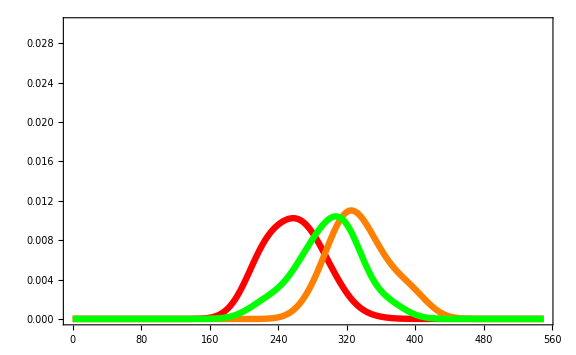
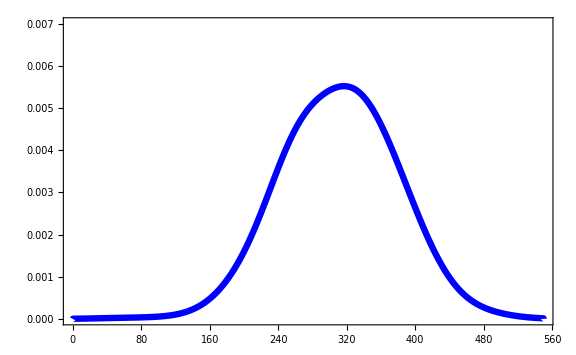

```mathematica
Overlay[{SmoothHistogram[Map[combliniptg1mm[[#]][[All,7]]&,{180,84,100}],20,PlotRange->{{0,550},{0,0.03}},PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Orange},{Thickness[0.008],Green}},ImageSize->Large,Frame->{True,False,False,False},FrameStyle->Directive[Black,25]],SmoothHistogram[Map[combliniptg1mm[[#]][[1,7]](*/3770*)&,Table[i,{i,Length[combliniptg1mm]}]],30,PlotRange->{{0,550},{0,0.007}},PlotStyle->{Thickness[0.008],Blue},ImageSize->Large,Frame->{True,False,False,False,False},FrameStyle->Directive[Black,25]]}]
```

```mathematica
{iptg1mmgrowthACF30minwindowsmooth,iptg1mmmcACF30minwindowsmooth,iptg1mmbetaxACF30minwindowsmooth,iptg1mmmcgrowthCCCF30minwindowsmooth,iptg1mmbetaxgrowthCCCF30minwindowsmooth,iptg1mmmcbetaxCCCF30minwindowsmooth}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\2022-2023\\microfluidic\\modeling files\\1mmiptgacfcccf30minwindowsmoothfull.txt","Table"];
```

```mathematica
GRbxCCF227smooth=Transpose@{Table[(i/60),{i,-(Length[iptg1mmbetaxgrowthCCCF30minwindowsmooth]-1)/2,(Length[iptg1mmbetaxgrowthCCCF30minwindowsmooth]-1)/2}],iptg1mmbetaxgrowthCCCF30minwindowsmooth};
```

```mathematica
GRmcCCF227smooth=Transpose@{Table[(i/60),{i,-(Length[iptg1mmmcgrowthCCCF30minwindowsmooth]-1)/2,(Length[iptg1mmmcgrowthCCCF30minwindowsmooth]-1)/2}],iptg1mmmcgrowthCCCF30minwindowsmooth};
```

```mathematica
mcbxCCF227smooth=Transpose@{Table[(i/60),{i,-(Length[iptg1mmmcbetaxCCCF30minwindowsmooth]-1)/2,(Length[iptg1mmmcbetaxCCCF30minwindowsmooth]-1)/2}],iptg1mmmcbetaxCCCF30minwindowsmooth};
```

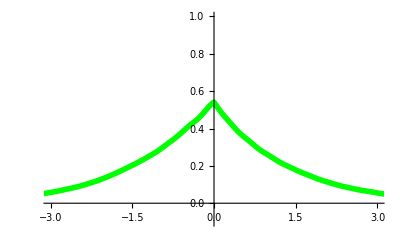

```mathematica
ListLinePlot[{mcbxCCF227smooth},PlotRange->{{-3,3},{-.1,1}},PlotStyle->{Directive[Thickness[0.01],Green]},AxesStyle->Directive[Black, 16]]
```

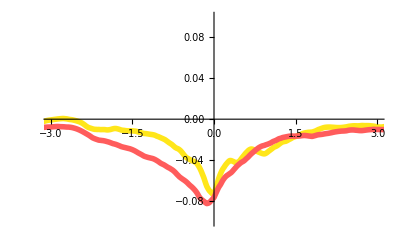

```mathematica
ListLinePlot[{GRbxCCF227smooth,GRmcCCF227smooth},PlotRange->{{-3,3},{-.1,0.1}},PlotStyle->{Directive[Thickness[0.01],RGBColor[1,0.9,0.1]],Directive[Thickness[0.01],RGBColor[1,0.36,0.36]]},AxesStyle->Directive[Black, 16]]
```

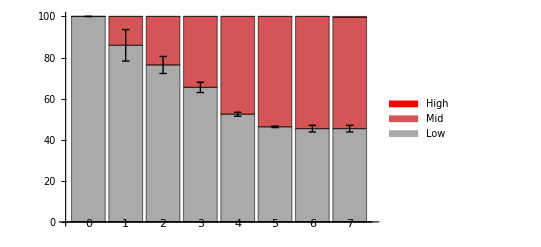

```mathematica
exp227transition=highlowtransitionovertime[combliniptg1mm];
exp630transition=highlowtransitionovertime[comblintest630];

avg=N[Mean[{100*exp630transition[[1]],100*exp227transition[[1]]}]]

bars=BarChart[avg,ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Red},.5],Red},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20},ChartLegends->{"Low","Mid","High"}];


errorGraphics=Graphics[Table[With[{x=i,yTop=avg1[[i]],err=error1[[i]]},{Line[{{x-0.1,yTop+err},{x+0.1,yTop+err}}],(*Top horizontal line*)Line[{{x,yTop-err},{x,yTop+err}}] (*Vertical line*),Line[{{x-0.1,yTop-err},{x+0.1,yTop-err}}]}],{i,Length[avg]}
]
];

(*Combine the bar chart with error bars*)
Show[bars,errorGraphics]
```

```mathematica
avghigh=N[Mean[{100*exp630transition[[2]],100*exp227transition[[2]]}]]
```

{{0.,0.,100.},{0.,16.2016,83.7984},{0.,30.6279,69.3721},{0.,41.7287,58.2713},{0.,58.8682,41.1318},{2.,67.969,30.031},{2.77519,74.9457,22.2791},{4.32558,76.1085,19.5659}}

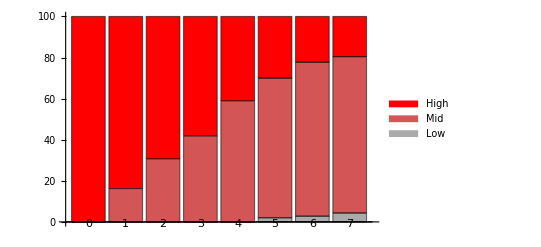

```mathematica
barshigh=BarChart[avghigh,ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Red},.5],Red},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20},ChartLegends->{"Low","Mid","High"}]
```

```mathematica
avg2=Map[avghigh[[#,2]]&,Range[1,8]]
```

{0.,16.2016,30.6279,41.7287,58.8682,67.969,74.9457,76.1085}

```mathematica
avg2low=Map[avghigh[[#,1]]&,Range[1,8]]
```

{0.,0.,0.,0.,0.,2.,2.77519,4.32558}

```mathematica
errorhigh=N[StandardDeviation[{100*exp630transition[[2]],100*exp227transition[[2]]}]]
```

{{0.,0.,0.},{0.,5.37182,5.37182},{0.,10.4257,10.4257},{0.,17.3543,17.3543},{0.,18.5711,18.5711},{2.82843,22.6713,25.4997},{1.73214,12.8047,14.5368},{0.460442,11.1602,10.6998}}

```mathematica
error2=Map[errorhigh[[#,2]]&,Range[1,8]]
```

{0.,5.37182,10.4257,17.3543,18.5711,22.6713,12.8047,11.1602}

```mathematica
error2low=Map[errorhigh[[#,1]]&,Range[1,8]]
```

{0.,0.,0.,0.,0.,2.82843,1.73214,0.460442}

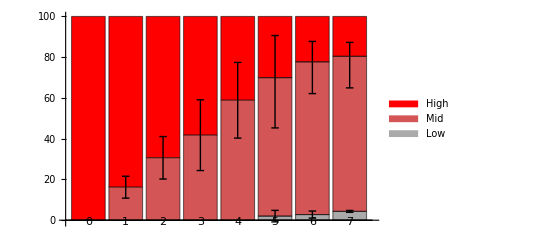

```mathematica
errorGraphicshigh=Graphics[Table[With[{x=i,yTop=avg2[[i]],err=error2[[i]],ylow=avg2low[[i]],errlow=error2low[[i]]
},
{Line[{{x-0.1,yTop+err},{x+0.1,yTop+err}}],(*Top horizontal line*)
Line[{{x,yTop-err},{x,yTop+err}}] (*Vertical line*),
Line[{{x-0.1,yTop-err},{x+0.1,yTop-err}}],
If[ylow!=0,
{Line[{{x-0.1,ylow+errlow},{x+0.1,ylow+errlow}}],(*Top horizontal line*)Line[{{x,ylow-errlow},{x,ylow+errlow}}] (*Vertical line*),Line[{{x-0.1,ylow-errlow},{x+0.1,ylow-errlow}}]}]}],{i,Length[avghigh]}
]
];


(*Combine the bar chart with error bars*)
Show[barshigh,errorGraphicshigh]
```

```mathematica
avgyfp=N[Mean[{100*exp630transition[[3]],100*exp227transition[[3]]}]]
```

{{100.,0.,0.},{72.6601,25.2189,2.12096},{56.4313,40.2573,3.31144},{32.5123,63.3826,4.10509},{21.1823,67.8845,10.9332},{8.867,78.2157,12.9174},{4.4335,81.4587,14.1078},{4.03667,81.4587,14.5047}}

```mathematica
avgyfp3=Map[avgyfp[[#,1]]&,Range[1,8]]
```

{100.,72.6601,56.4313,32.5123,21.1823,8.867,4.4335,4.03667}

```mathematica
avgyfp4=Map[avgyfp[[#,2]]&,Range[1,8]]
```

{0.,25.2189,40.2573,63.3826,67.8845,78.2157,81.4587,81.4587}

```mathematica
avgyfp3high=avgyfp4+avgyfp3
```

{100.,97.879,96.6886,95.8949,89.0668,87.0826,85.8922,85.4953}

```mathematica
erroryfp=N[StandardDeviation[{100*exp630transition[[3]],100*exp227transition[[3]]}]]
```

{{0.,0.,0.},{11.8432,13.7203,1.8771},{7.97285,8.16637,0.193516},{4.52827,5.45715,0.928876},{10.4499,3.96707,6.48278},{7.66323,3.98643,3.6768},{3.83161,1.8384,1.99321},{3.27042,1.8384,1.43202}}

```mathematica
erroryfp3=Map[erroryfp[[#,1]]&,Range[1,8]]
```

{0.,11.8432,7.97285,4.52827,10.4499,7.66323,3.83161,3.27042}

```mathematica
erroryfp3high=Map[erroryfp[[#,3]]&,Range[1,8]]
```

{0.,1.8771,0.193516,0.928876,6.48278,3.6768,1.99321,1.43202}

```mathematica
baryfplow=BarChart[avgyfp,ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Yellow},.5],Yellow},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20},ChartLegends->{"Low","Mid","High"}];
```

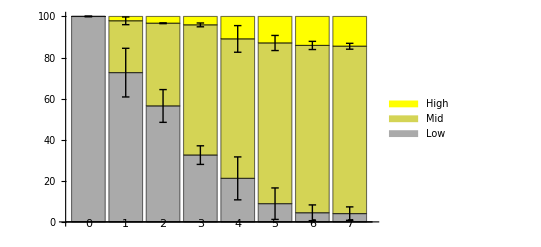

```mathematica
errorGraphicsyfplow=Graphics[Table[With[{x=i,yTop=avgyfp3[[i]],err=erroryfp3[[i]],yTophigh=avgyfp3high[[i]],errhigh=erroryfp3high[[i]]},
{Line[{{x-0.1,yTop+err},{x+0.1,yTop+err}}],
Line[{{x-0.1,yTophigh+errhigh},{x+0.1,yTophigh+errhigh}}],(*Top horizontal line*)
Line[{{x,yTop-err},{x,yTop+err}}] (*Vertical line*),
Line[{{x,yTophigh-errhigh},{x,yTophigh+errhigh}}],
Line[{{x-0.1,yTophigh-errhigh},{x+0.1,yTophigh-errhigh}}],
Line[{{x-0.1,yTop-err},{x+0.1,yTop-err}}]}],{i,Length[avghigh]}
]
];


(*Combine the bar chart with error bars*)
Show[baryfplow,errorGraphicsyfplow]
```

```mathematica
avgyfplow=N[Mean[{100*exp630transition[[4]],100*exp227transition[[4]]}]]
```

{{0.,0.,100.},{3.40909,36.9697,59.6212},{10.6061,44.0909,45.303},{13.0303,52.9545,34.0152},{13.7879,64.4697,21.7424},{15.8333,76.2121,7.95455},{15.8333,81.8939,2.27273},{16.5909,81.5152,1.89394}}

```mathematica
avgyfp5=Map[avgyfplow[[#,1]]&,Range[1,8]]
```

{0.,3.40909,10.6061,13.0303,13.7879,15.8333,15.8333,16.5909}

```mathematica
avgyfp6=Map[avgyfplow[[#,2]]&,Range[1,8]]
```

{0.,36.9697,44.0909,52.9545,64.4697,76.2121,81.8939,81.5152}

```mathematica
avgyfp5low=avgyfp5+avgyfp6
```

{0.,40.3788,54.697,65.9848,78.2576,92.0455,97.7273,98.1061}

```mathematica
erroryfplow=N[StandardDeviation[{100*exp630transition[[4]],100*exp227transition[[4]]}]]
```

{{0.,0.,0.},{4.82118,9.85664,14.6778},{3.21412,1.28565,1.92847},{1.92847,5.24973,3.32126},{2.99985,17.2491,14.2493},{1.17851,12.4279,11.2494},{1.17851,4.39263,3.21412},{2.24989,4.92832,2.67843}}

```mathematica
erroryfp5=Map[erroryfplow[[#,1]]&,Range[1,8]]
```

{0.,4.82118,3.21412,1.92847,2.99985,1.17851,1.17851,2.24989}

```mathematica
erroryfp6high=Map[erroryfplow[[#,3]]&,Range[1,8]]
```

{0.,14.6778,1.92847,3.32126,14.2493,11.2494,3.21412,2.67843}

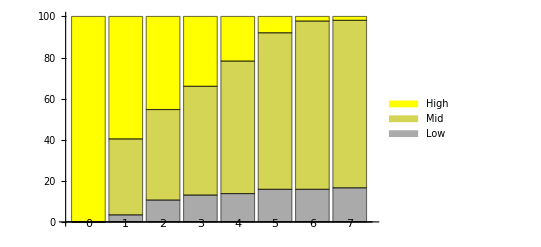

```mathematica
baryfphigh=BarChart[avgyfplow,ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Yellow},.5],Yellow},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20},ChartLegends->{"Low","Mid","High"}]
```

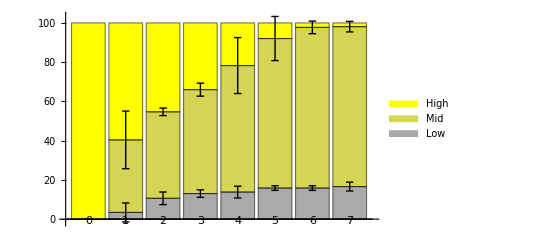

```mathematica
errorGraphicsyfphigh=Graphics[Table[With[{x=i,yTop=avgyfp5[[i]],err=erroryfp5[[i]],yTophigh=avgyfp5low[[i]],errhigh=erroryfp6high[[i]]},
{Line[{{x-0.1,yTop+err},{x+0.1,yTop+err}}],
Line[{{x-0.1,yTophigh+errhigh},{x+0.1,yTophigh+errhigh}}],(*Top horizontal line*)
Line[{{x,yTop-err},{x,yTop+err}}] (*Vertical line*),
Line[{{x,yTophigh-errhigh},{x,yTophigh+errhigh}}],
Line[{{x-0.1,yTophigh-errhigh},{x+0.1,yTophigh-errhigh}}],
Line[{{x-0.1,yTop-err},{x+0.1,yTop-err}}]}],{i,Length[avghigh]}
]
];


(*Combine the bar chart with error bars*)
Show[baryfphigh,errorGraphicsyfphigh]
```